tamoaltas - Difracción en una Esfera

```mathematica
LommelU[n_,u_,v_, l_] := Sum[(-1)^m (u/v)^(n+2m) BesselJ[n+2m,v],{m,0,l}]
LommelV[n_,u_,v_, l_] := Sum[(-1)^m (u/v)^(-n-2m) BesselJ[-n-2m,v],{m,0,l}]
```

```mathematica
Isom[u_,v_,l_] := LommelV[0,u,v,l]^2 + LommelV[1,u,v,l]^2
```

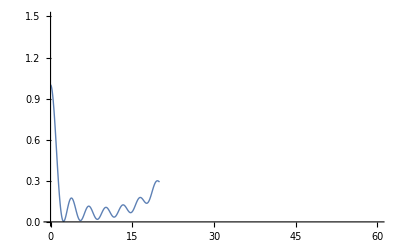

```mathematica
u = 20; l = 15;
Plot[Isom[u,v,l],
{v,0,u},
PlotStyle->Thick,
PlotLegends->"Región de Sombra",
PlotRange->{{0,3u},{0,1.5}}]
```

```mathematica
Iilum[u_,v_,l_] :=  1 + LommelU[1,u,v,l]^2 + LommelU[2,u,v,l]^2 - 2LommelU[1,u,v,l]Sin[(u^2+v^2)/(2u)] + 2LommelU[2,u,v,l]Cos[(u^2+v^2)/(2u)]
```

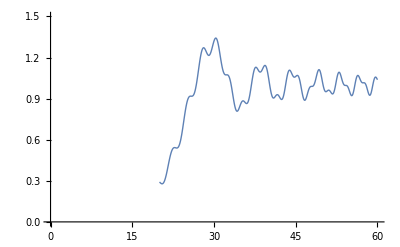

```mathematica
Plot[Iilum[u,v,l],
{v,u,3u},
PlotStyle->Thick,
PlotLegends->"Región de Luz",
PlotRange->{{0,3u},{0,1.5}}]
```

```mathematica
ambas[u_,v_,l_]:=Piecewise[{{Isom[u,v,l],0<=v<= u},{Iilum[u,v,l],u <= v < 3u}}]
```

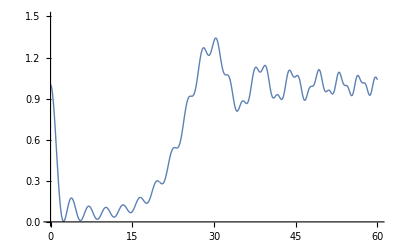

```mathematica
graficas  =Plot[ambas[u,v,l],
{v,0,3u},
PlotStyle->Thick,
PlotLegends->None,
PlotRange->{{0,3u},{0,1.5}}]
```

```mathematica
Rasterize[graficas, ImageResolution-> 300]
```

-Graphics-

```mathematica
Iambas[x_,y_, u_, l_] := ambas[u,Sqrt[x^2+y^2],l]
```

```mathematica
plot = DensityPlot[Iambas[x,y,u,l],{x,-3u,3u},{y,-3u,3u},ColorFunction->"SunsetColors",PlotLegends->Automatic, PlotPoints->300]
```

-Graphics-

```mathematica
imagesDir=FileNameJoin[{NotebookDirectory[],"/images" }];
plotName= StringJoin[ {FileBaseName[NotebookFileName[]], ".png"}];
filePath= FileNameJoin[{imagesDir,plotName}];

(* Se crea el directorio si no existe *)
If[!DirectoryQ[imagesDir],CreateDirectory[imagesDir]];

Rasterize[plot,ImageResolution->Automatic,Background->White];
```

```mathematica
Export[filePath,plot,ImageResolution->Automatic];
```